# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-4,30-4}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

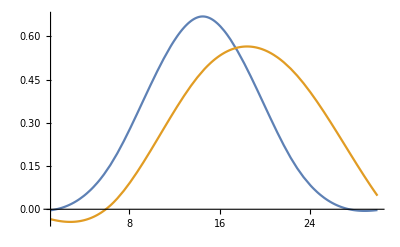

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

n=1;

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=1*dfline1'[p1];
fric2=1*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<n,Return[{v1,v2,"sign",e+1}],Return[{0.,0.,"sign",e}]]];

(* magnitud *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<n,Return[{v1,v2,"mag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.01,"converged","ok"],e}

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)

PyrUpgrade1D[{v1_,v2_,status_,n},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{0.,0.,status,n}];

PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.2,3.,"ok",0.};
i=0;
p=10.;
```

```mathematica
n=3;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,noteBookMode]
```

{0.99349,2.86729,ok,0.}

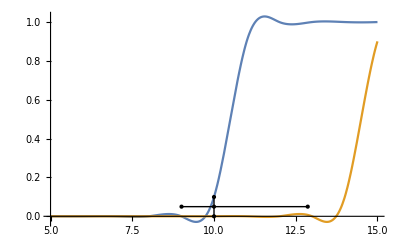

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)

newValues[i_,{v1_,v2_,status_},newv0_,"ConstrainedNewMethod"]:=Block[{v,r,rs},(
v=v1+v2;

If[v≠0. && status=="ok",
Table[
r=RandomReal[];
{r,1-r}*v
,{j,i}]
,
newv0
]

)]
```

```mathematica
(* We create the list of values in case v=0 *)
r=RandomReal[];
rangev0=Range[0,5,0.2];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];
```

```mathematica
nV=newValues[10,{0.,0.,"sign"},newv0,"ConstrainedNewMethod"]
Total/@nV
```

{{0.,0.},{0.123016,0.0769838},{0.246032,0.153968},{0.369048,0.230952},{0.492065,0.307935},{0.615081,0.384919},{0.738097,0.461903},{0.861113,0.538887},{0.984129,0.615871},{1.10715,0.692855},{1.23016,0.769838},{1.35318,0.846822},{1.47619,0.923806},{1.59921,1.00079},{1.72223,1.07777},{1.84524,1.15476},{1.96826,1.23174},{2.09127,1.30873},{2.21429,1.38571},{2.33731,1.46269},{2.46032,1.53968},{2.58334,1.61666},{2.70636,1.69364},{2.82937,1.77063},{2.95239,1.84761},{3.0754,1.9246},{0.,0.},{0.0769838,0.123016},{0.153968,0.246032},{0.230952,0.369048},{0.307935,0.492065},{0.384919,0.615081},{0.461903,0.738097},{0.538887,0.861113},{0.615871,0.984129},{0.692855,1.10715},{0.769838,1.23016},{0.846822,1.35318},{0.923806,1.47619},{1.00079,1.59921},{1.07777,1.72223},{1.15476,1.84524},{1.23174,1.96826},{1.30873,2.09127},{1.38571,2.21429},{1.46269,2.33731},{1.53968,2.46032},{1.61666,2.58334},{1.69364,2.70636},{1.77063,2.82937},{1.84761,2.95239},{1.9246,3.0754},{0.,0.},{0.2,0.},{0.4,0.},{0.6,0.},{0.8,0.},{1.,0.},{1.2,0.},{1.4,0.},{1.6,0.},{1.8,0.},{2.,0.},{2.2,0.},{2.4,0.},{2.6,0.},{2.8,0.},{3.,0.},{3.2,0.},{3.4,0.},{3.6,0.},{3.8,0.},{4.,0.},{4.2,0.},{4.4,0.},{4.6,0.},{4.8,0.},{5.,0.},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.},{0.,1.2},{0.,1.4},{0.,1.6},{0.,1.8},{0.,2.},{0.,2.2},{0.,2.4},{0.,2.6},{0.,2.8},{0.,3.},{0.,3.2},{0.,3.4},{0.,3.6},{0.,3.8},{0.,4.},{0.,4.2},{0.,4.4},{0.,4.6},{0.,4.8},{0.,5.}}

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.}

```mathematica
(* This will give back a value that converged or is on "ok" status. If not, error is returned and {v1,v2} goes back to 0. *)

pickNewValue[tableNewVals_,"ConstrainedNewMethod"]:=Block[{newValCon,newValAny},(

newValCon=Select[tableNewVals,(#[[3]]==("converged")&& #[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];
newValAny=Select[tableNewVals,(#[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];

If[newValCon=={}&&newValAny=={},
tableNewVals[[1]]
,

If[newValCon=={},

If[newValAny[[1,3]]!="converged",
newValAny[[1]],
Flatten[{0.,0.,"fakeconverged",newValAny[[1,4]]+1}]
],

newValCon[[1]]
]

]
)]
```

```mathematica
threshold=0.001;
n=3;
p0=10;
i=10;

updateValues={0.,0.,"ok",0.};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)

nV=newValues[10,updateValues[[1;;3]],newv0,"ConstrainedNewMethod"];

tableNV=Table[
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),noteBookMode]

,{j,1,i}];

tValues
,{v,nV}];

sol=pickNewValue[tableNV,"ConstrainedNewMethod"]
```

{0.0965616,3.88725,converged,0.}

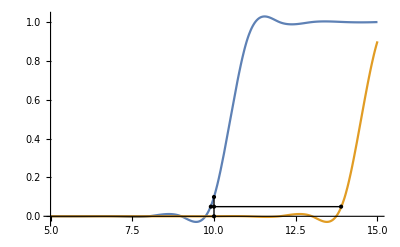

```mathematica
(* see *)
seePlot[p0,5,sol[[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_,listv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c, updateValues,nV,tableNewValues,tValues},(

n=1;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Do[


(* Flag to stop when e≥n *)
If[updateValues[[4]]<n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;3]],listv0,"ConstrainedNewMethod"];
(* compute at this scale, using current motion estimate *)


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]

,{j,1,i}];
tValues
,{v,nV}];

(* We only update updateValues with the tValue that converged *)
updateValues=pickNewValue[tableNewValues,"ConstrainedNewMethod"];

c=c-1;
,{f,1,Length[pyrfunctions]}];

updateValues[[1;;3]]
)];
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=10;
p=15;

(* m-> max lvl, n-> min lvl *)
m=1;
n=3;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,newv0,pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

{3.9173,0.0827004,converged}

{4.,converged}

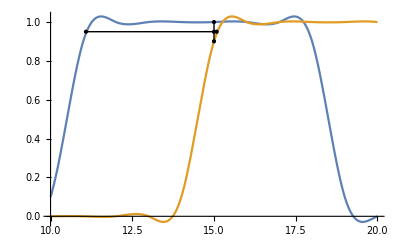

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

{{0.00211626,0.497884,mag,1},{0.00211626,0.497884,sign,2},{0.00211626,0.497884,sign,3},{0.00211626,0.497884,sign,4},{0.00211626,0.497884,mag,5},{3.1245,0.876344,mag,6},{0.993038,3.00722,converged,7},{1.0068,2.9932,converged,8},{0.994953,3.00505,converged,9},{3.28398,0.716021,mag,10},{0.553809,3.44619,converged,11},{1.5,2.5,converged,12},{2.5,1.5,converged,13},{3.44618,0.553818,converged,14},{3.88247,0.117531,converged,15},{0.999854,3.00015,converged,16},{1.00287,2.99713,converged,17},{1.37581,2.6242,mag,18},{0.553818,3.44618,converged,19},{1.5,2.5,converged,20},{2.5,1.5,converged,21},{3.44619,0.553809,converged,22},{2.61315,1.38654,mag,23},{3.00272,0.997372,converged,24},{3.00856,0.991448,converged,25},{3.00474,0.995678,converged,26},{0.00211626,0.497884,mag,27},{0.00211626,0.497884,sign,28},{0.00211626,0.497884,sign,29},{0.00211626,0.497884,sign,30}}

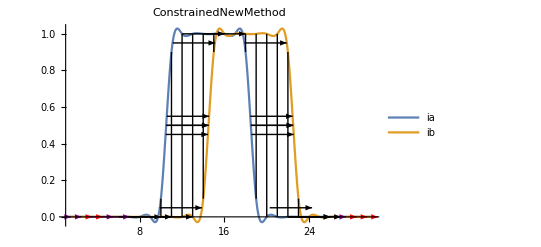

```mathematica
r=RandomReal[];
rangev0=Range[0,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[newv0,Range[1,Length[line1]],pyrf12[[1;;3]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[newv0,Range[1,30],pyrf12[[1;;3]],0.001,noteBookMode]
```

```mathematica
ListAnimate[pixelIterGraphics[10,15,newv0,4, 4,pyrf12[[3;;4]],0.001,"ConstrainedNewMethod"]];
```

## Graphics for One pixel

```mathematica
pickNewValueIter[tableIterNewVals_,"ConstrainedNewMethod"]:=Block[{newIterValCon,newIterValAny},(
newIterValCon=Select[tableIterNewVals,(Last[#][[3]]==("converged")&&Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];
newIterValAny=Select[tableIterNewVals,(Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];

If[newIterValCon=={}&&newIterValAny=={},
tableIterNewVals[[1]]
,

If[newIterValCon=={},

If[Last[newIterValAny[[1]]][[3]]≠"converged",
newIterValAny[[1]],
Join[newIterValAny[[1]],{Flatten[{0.,0.,"fakeconverged",Last[newIterValAny[[1]]][[4]]+1}]}]
]
,
newIterValCon[[1]]
]

]

)]
```

```mathematica
i=10;
p0=10;
threshold=0.001;
n=3;
updateValues={0.,0.,"ok",0.};
```

```mathematica
(* Flag to stop when e≥2 *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 5 and -5 *)
nV=newValues[10,updateValues[[1;;3]],newv0,"ConstrainedNewMethod"];

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"][[All,1;;3]]

Last[goodValIter]
```

{{0.0243943,3.61968,ok},{0.0430796,3.69344,ok},{0.0573774,3.74517,ok},{0.068307,3.78285,ok},{0.0766545,3.81078,ok},{0.0830253,3.83168,ok},{0.0878844,3.84741,ok},{0.0915886,3.85928,ok},{0.0944114,3.86826,converged},{0.0965616,3.87506,converged}}

{0.0965616,3.87506,converged}

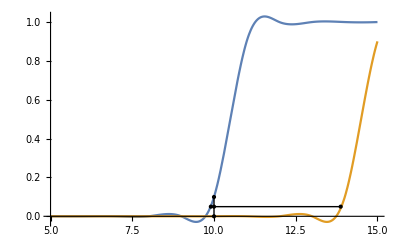

```mathematica
(* see *)
seePlot[p0,5,Last[goodValIter][[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,newv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,tValues,iterTable,goodValIter,nV},(

n=1;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Table[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;3]],newv0,"ConstrainedNewMethod"];


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"];
updateValues=Last[goodValIter];

goodValIter[[All,1;;3]]
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;3]],0.001,noteBookMode]
,{p,1,30}]
```

{{0.26267,0.23733,mag},{0.26267,0.23733,mag},{0.26267,0.23733,mag},{0.26267,0.23733,mag},{0.26267,0.23733,mag},{1.76923,2.23161,mag},{0.99218,3.00788,converged},{1.99349,2.00653,converged},{2.0126,1.9874,converged},{1.25242,2.74758,ok},{0.553809,3.44619,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44618,0.553818,converged},{3.88173,0.118266,converged},{1.99133,2.00867,converged},{1.99559,2.00441,converged},{0.125603,3.87434,converged},{0.553818,3.44618,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44619,0.553809,converged},{2.61372,1.38627,mag},{0.995556,3.00432,converged},{3.97565,0.0243951,converged},{1.6835,2.33224,mag},{0.26267,0.23733,sign},{0.26267,0.23733,sign},{0.26267,0.23733,sign},{0.26267,0.23733,sign}}

```mathematica
Table[
PyrFlow1DIter[10,p,newv0, pyrf12[[1;;3]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{{0.26267,0.23733,mag},{0.26267,0.23733,mag},{0.26267,0.23733,mag},{2.73177,1.27988,mag},{0.26267,0.23733,mag},{0.00163929,3.99843,converged},{1.00109,2.999,converged},{0.989356,3.01065,converged},{1.98906,2.01094,converged},{0.120616,3.87938,converged},{0.553809,3.44619,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44618,0.553818,converged},{3.90028,0.0997242,converged},{0.998934,3.00107,converged},{1.99909,2.00091,converged},{0.11725,3.88275,converged},{0.553818,3.44618,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44619,0.553809,converged},{2.89512,1.10491,ok},{1.97917,2.02077,converged},{3.9834,0.0161972,converged},{3.00362,0.993639,converged},{0.26267,0.23733,mag},{0.26267,0.23733,sign},{0.26267,0.23733,sign},{0.26267,0.23733,sign}}

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]==PyrFlow1DIter[10,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{True,True,True,False,False,False,False,False,False,False,False,True,True,False,True,True,True,False,False,True,True,False,False,False,False,False,False,False,False,True}

#### Test

```mathematica
(* List of initial values we are going to try *)
newv0;
```

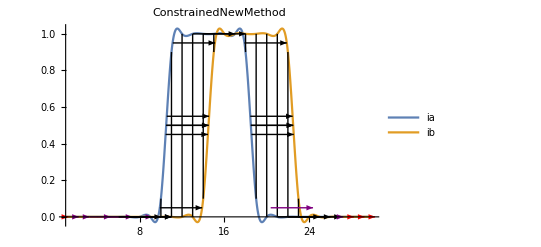

```mathematica
seeAllLine[newv0,Range[1,30],pyrf12[[1;;3]],0.001,noteBookMode]
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[-5,5,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

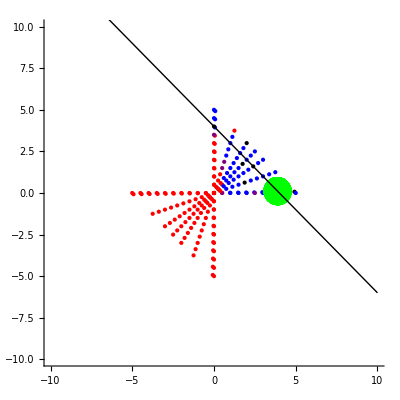
-Graphics-ConstrainedNewMethod

```mathematica
lvlmin=1;
lvlmax=3;
p=15;
dis=4;

mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,p,listv0,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";

(*pixelInitialValueGraphics[10,1000,p,{-10,10},dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]*)
```